### Load FeynCalc

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/cristiansierra/Documents/PostDoc_Research/Projects/e+e-->Zh_NLO/Mathematica code

```mathematica
Global`$LoadAddOns={"FeynHelpers"};
$LoadFeynArts=True;
<<FeynCalc`
$FAVerbose=0;
$CKM=True;
```

FeynCalc 10.0.0 (dev version). For help, use the online documentation, check out the wiki or visit the forum.

Please check our FAQ for answers to some common FeynCalc questions and have a look at the supplied examples.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

FeynHelpers 2.0.0 (), for more information see the accompanying publication.

Have a look at the supplied examples. If you use FeynHelpers in your research, please evaluate FeynHelpersHowToCite[] to learn how to correctly cite this work.

FeynArts 3.11 (25 Mar 2022) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

```mathematica
FAPatch[PatchModelsOnly->True]
```

Successfully patched FeynArts.

### Self-energies

#### H

```mathematica
HTopo=CreateTopologies[1,1->1,ExcludeTopologies->{AllBoxes,Triangles}];
```

```mathematica
HDiag=InsertFields[HTopo,{S[1]}->{S[1]},Model->{"tripletSM"},
GenericModel->{"tripletSM"},InsertionLevel->{Particles},
ExcludeParticles->{S[1],V[1|2|3|4],U[1|2|3|4|11|12|31|32],F[_,{_}]}];
```

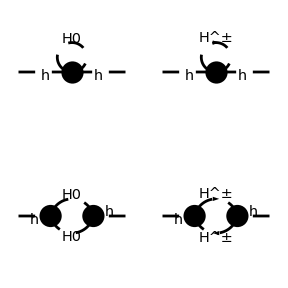

```mathematica
Paint[HDiag,ColumnsXRows->{2,2},Numbering->None];
```

```mathematica
HAmps=FCFAConvert[CreateFeynAmp[HDiag,PreFactor->-I/(2Pi)^D,Truncated->True],
IncomingMomenta->{k},OutgoingMomenta->{k},TransversePolarizationVectors->{k},
Contract->True,LoopMomenta->{q},ChangeDimension->D,
UndoChiralSplittings->True,List->False,DropSumOver->False,
LorentzIndexNames->{µ,ν}]/.lam3->Subscript[λ, 3]/.MH0->Subscript[M, H]/.MHch->Subscript[M, H]/.FCGV[x_String]:>ToExpression[x]//
DiracSimplify[#,DiracSubstitute67->True]&//FCGVToSymbol//DiracSimplify;
```

```mathematica
(*When setting to True the following command rewrites A0 in terms of B0*)
```

```mathematica
SetOptions[A0,A0ToB0->False];
```

```mathematica
(*Tensor decomposition into Passarino Veltman functions:*)
```

```mathematica
HAmpsDec=  TID[HAmps,q,UsePaVeBasis->True,ToPaVe->True]//DiracSimplify;
```

```mathematica
ΣH=HAmpsDec//FCReplaceD[#,D->4-2Epsilon]&//Series[#,{Epsilon,0,0}]&//Normal//ChangeDimension[#,4]&;
```

```mathematica
ΣH//FullSimplify//TraditionalForm
```

(3 λ_3 (λ_3 v^2 B_0((k̄)^2,M_H^2,M_H^2)+A_0(M_H^2)))/(32 π^2)

```mathematica
FCHideEpsilon[PaXEvaluate[ΣH,PaXSeries->{{k ,0,0}},PaXAnalytic->True]]//FullSimplify//TraditionalForm
```

(3 λ_3 (M_H^2 (Δ+log(μ^2/(4 π^2 M_H^2))+1)+λ_3 v^2 (Δ+log(μ^2/(4 π^2 M_H^2)))))/(32 π^2)

#### ZZ

```mathematica
ZZTopo=CreateTopologies[1,1->1,ExcludeTopologies->{AllBoxes,Triangles}];
```

```mathematica
ZZDiag=InsertFields[ZZTopo,{V[2]}->{V[2]},Model->{"tripletSM"},GenericModel->{"tripletSM"},InsertionLevel->{Particles},ExcludeParticles->{S[Except[6]],V[1|3|4],U[1|2|3|4|11|12|31|32],F[_,{_}]}];
```

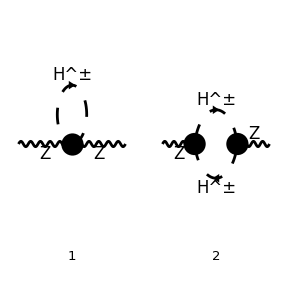

```mathematica
Paint[ZZDiag,ColumnsXRows->{2,1},Numbering->Simple];
```

```mathematica
ZZAmps=DiracSimplify[FCFAConvert[CreateFeynAmp[ZZDiag,PreFactor->-I/(2Pi)^D,Truncated->True],IncomingMomenta->{k},OutgoingMomenta->{k},TransversePolarizationVectors->{k},Contract->True,LoopMomenta->{q},ChangeDimension->D,UndoChiralSplittings->True,List->False,DropSumOver->False,LorentzIndexNames->{µ,ν}]/.FCGV[x_String]:>ToExpression[x],DiracSubstitute67->True]/.gc38->(FCGV["CW"]*FCGV["EL"])/FCGV["SW"]//DiracSimplify//FCGVToSymbol;
```

```mathematica
(*Tensor decomposition into Passarino Veltman functions:*)
```

```mathematica
ΣZZ= TID[ZZAmps/.EL->g Sin[Subscript[θ, w]]/.SW->Sin[Subscript[θ, w]]/.CW->Cos[Subscript[θ, w]]/.MH0->Subscript[M, H0]/.MHch->Subscript[M, Hp],q,UsePaVeBasis->True,ToPaVe->True]//DiracSimplify;
```

```mathematica
(*ΣZZ=ΣZZ/.EL->g Sin[Subscript[θ, w]]/.SW->Sin[Subscript[θ, w]]/.CW->Cos[Subscript[θ, w]]/.MH0->Subscript[M, H0]/.MHch->Subscript[M, Hp]//FCReplaceD[#,D->4-2Epsilon]&//Series[#,{Epsilon,0,0}]&//Normal//ChangeDimension[#,4]&;*)
```

```mathematica
SetOptions[A0,A0ToB0->True];
```

```mathematica
(*Projecting out the transverse part, definition from hep-ph/0612057 Eq.50 ΣZZ= (-gµν+kµkν/k^2)ΣZZT + (kµkν/k^2) ΣZZL*)
```

```mathematica
ΣZZT=(2Pi)^(-4)(1/3)PaVeLimitTo4[(-Pair[LorentzIndex[ν],LorentzIndex[µ]]ΣZZ+(Pair[LorentzIndex[ν],Momentum[k]] Pair[LorentzIndex[µ],Momentum[k]]/Pair[Momentum[k],Momentum[k]])ΣZZ)(2Pi)^D]//Contract;
```

```mathematica
% //FullSimplify//TraditionalForm
```

(g^2 cos^2(θ_w) (12 M_Hp^2 (B_0(0,M_Hp^2,M_Hp^2)-B_0((k̄)^2,M_Hp^2,M_Hp^2))+(k̄)^2 (3 B_0((k̄)^2,M_Hp^2,M_Hp^2)+2)))/(144 π^2)

#### γZ

```mathematica
γZTopo=CreateTopologies[1,1->1,ExcludeTopologies->{AllBoxes,Triangles}];
```

```mathematica
γZDiag=InsertFields[γZTopo,{V[1]}->{V[2]},Model->{"tripletSM"},GenericModel->{"tripletSM"},InsertionLevel->{Particles},ExcludeParticles->{S[Except[6]],V[1|3|4],U[1|2|3|4|11|12|31|32],F[_,{_}]}];
```

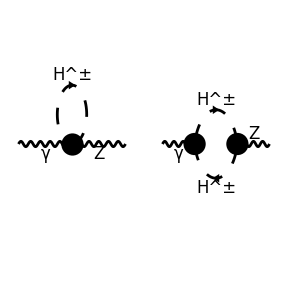

```mathematica
Paint[γZDiag,ColumnsXRows->{2,1},Numbering->None];
```

```mathematica
γZAmps=DiracSimplify[FCFAConvert[CreateFeynAmp[γZDiag,PreFactor->-I/(2Pi)^D,Truncated->True],IncomingMomenta->{k},OutgoingMomenta->{k},TransversePolarizationVectors->{k},Contract->True,LoopMomenta->{q},ChangeDimension->D,UndoChiralSplittings->True,List->False,DropSumOver->False,LorentzIndexNames->{µ,ν}]/.FCGV[x_String]:>ToExpression[x],DiracSubstitute67->True]/.gc11->FCGV["EL"]/.gc38->(FCGV["CW"]*FCGV["EL"])/FCGV["SW"]//DiracSimplify//FCGVToSymbol/.EL->g Sin[Subscript[θ, w]]/.SW->Sin[Subscript[θ, w]]/.CW->Cos[Subscript[θ, w]];
```

```mathematica
(*Tensor decomposition into Passarino Veltman functions:*)
```

```mathematica
γZAmpsDec= TID[γZAmps,q,UsePaVeBasis->True,ToPaVe->True]//DiracSimplify;
```

```mathematica
(*SetOptions[A0,A0ToB0->True];*)
```

```mathematica
ΣγZ=γZAmpsDec/.MHch->Subscript[M, Hp];
```

```mathematica
(*Projecting out the transverse part*)
```

```mathematica
ΣγZT=(2Pi)^(-4)(1/3)PaVeLimitTo4[(2Pi)^D(-Pair[LorentzIndex[ν],LorentzIndex[µ]]ΣγZ+(Pair[LorentzIndex[ν],Momentum[k]] Pair[LorentzIndex[µ],Momentum[k]]/Pair[Momentum[k],Momentum[k]])ΣγZ)]//Contract;
```

```mathematica
%//FullSimplify//TraditionalForm
```

(CW EL^2 (12 M_Hp^2 (B_0(0,M_Hp^2,M_Hp^2)-B_0((k̄)^2,M_Hp^2,M_Hp^2))+(k̄)^2 (3 B_0((k̄)^2,M_Hp^2,M_Hp^2)+2)))/(144 π^2 SW)

#### γγ

```mathematica
γγTopo=CreateTopologies[1,1->1,ExcludeTopologies->{AllBoxes,Triangles}];
```

```mathematica
γγDiag=InsertFields[γγTopo,{V[1]}->{V[1]},Model->{"tripletSM"},GenericModel->{"tripletSM"},InsertionLevel->{Particles},ExcludeParticles->{S[Except[6]],V[1|3|4],U[1|2|3|4|11|12|31|32],F[_,{_}]}];
```

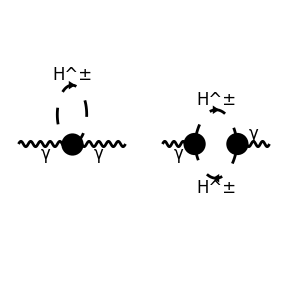

```mathematica
Paint[γγDiag,ColumnsXRows->{2,1},Numbering->None];
```

```mathematica
γγAmps=DiracSimplify[FCFAConvert[CreateFeynAmp[γγDiag,PreFactor->-I/(2Pi)^D,Truncated->True],IncomingMomenta->{k},OutgoingMomenta->{k},TransversePolarizationVectors->{k},Contract->True,LoopMomenta->{q},ChangeDimension->D,UndoChiralSplittings->True,List->False,DropSumOver->False,LorentzIndexNames->{µ,ν}]/.FCGV[x_String]:>ToExpression[x],DiracSubstitute67->True]/.gc11->FCGV["EL"]//DiracSimplify//FCGVToSymbol/.EL->g Sin[Subscript[θ, w]]/.SW->Sin[Subscript[θ, w]]/.CW->Cos[Subscript[θ, w]];
```

```mathematica
(*Tensor decomposition into Passarino Veltman functions:*)
```

```mathematica
γγAmpsDec= TID[γγAmps,q,UsePaVeBasis->True,ToPaVe->True]//DiracSimplify;
```

```mathematica
(*SetOptions[A0,A0ToB0->True];*)
```

```mathematica
Σγγ=γγAmpsDec/.MHch->Subscript[M, Hp];
```

```mathematica
(*Projecting out the transverse part*)
```

```mathematica
ΣγγT=(2Pi)^(-4)(1/3)PaVeLimitTo4[(-Pair[LorentzIndex[ν],LorentzIndex[µ]]Σγγ+(Pair[LorentzIndex[ν],Momentum[k]] Pair[LorentzIndex[µ],Momentum[k]]/Pair[Momentum[k],Momentum[k]])Σγγ)(2Pi)^D]//Contract;
```

```mathematica
%//FullSimplify//TraditionalForm
```

(EL^2 (12 M_Hp^2 (B_0(0,M_Hp^2,M_Hp^2)-B_0((k̄)^2,M_Hp^2,M_Hp^2))+(k̄)^2 (3 B_0((k̄)^2,M_Hp^2,M_Hp^2)+2)))/(144 π^2)

#### WW

```mathematica
WWTopo=CreateTopologies[1,1->1,ExcludeTopologies->{AllBoxes,Triangles}];
```

```mathematica
WWDiag=InsertFields[WWTopo,{V[3]}->{V[3]},Model->{"tripletSM"},GenericModel->{"tripletSM"},InsertionLevel->{Particles},ExcludeParticles->{S[1],V[1|2|3|4],U[1|2|3|4|11|12|31|32],F[_,{_}]}];
```

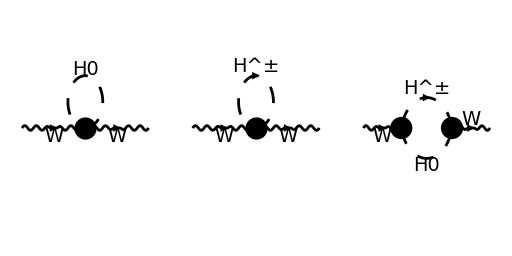

```mathematica
Paint[WWDiag,ColumnsXRows->{3,1},Numbering->None,ImageSize->{512,256}];
```

```mathematica
WWAmps=DiracSimplify[FCFAConvert[CreateFeynAmp[WWDiag,PreFactor->-I/(2Pi)^D,Truncated->True],IncomingMomenta->{k},OutgoingMomenta->{k},TransversePolarizationVectors->{k},Contract->True,LoopMomenta->{q},ChangeDimension->D,UndoChiralSplittings->True,List->False,DropSumOver->False,LorentzIndexNames->{µ,ν}]/.FCGV[x_String]:>ToExpression[x],DiracSubstitute67->True]/.gc28->(FCGV["EL"])/FCGV["SW"]/.gc24->-((FCGV["EL"])/FCGV["SW"])//DiracSimplify//FCGVToSymbol/.SW->Sin[Subscript[θ, w]]/.CW->Cos[Subscript[θ, w]]/.EL->g Sin[Subscript[θ, w]];
```

```mathematica
(*Tensor decomposition into Passarino Veltman functions:*)
```

```mathematica
WWAmpsDec= TID[WWAmps,q,UsePaVeBasis->True,ToPaVe->True]//DiracSimplify;
```

```mathematica
(*SetOptions[A0,A0ToB0->True];*)
```

```mathematica
ΣWW=WWAmpsDec/.MH0->Subscript[M, H]/.MHch->Subscript[M, Hp];
```

```mathematica
ΣWWT=(1/3)(2Pi)^(-4)PaVeLimitTo4[(-Pair[LorentzIndex[ν],LorentzIndex[µ]]ΣWW+(Pair[LorentzIndex[ν],Momentum[k]] Pair[LorentzIndex[µ],Momentum[k]]/Pair[Momentum[k],Momentum[k]])ΣWW)(2Pi)^D]//Contract;
```

```mathematica
%/.Subscript[M, Hp]->Subscript[M, H]//FullSimplify//TraditionalForm
```

(EL^2 (12 M_H^2 (B_0(0,M_H^2,M_H^2)-B_0((k̄)^2,M_H^2,M_H^2))+(k̄)^2 (3 B_0((k̄)^2,M_H^2,M_H^2)+2)))/(144 π^2 SW^2)

### Higgsstrahlung

#### LO

```mathematica
topoLO=CreateTopologies[0,2->2];
diagLO=InsertFields[topoLO,{-F[2,{1}],F[2,{1}]}->{V[2],S[1]},Model->{"tripletSM"},GenericModel->{"tripletSM"},InsertionLevel->{Particles},ExcludeParticles->{S[1],S[2],V[3|4],U[1|2|3|4|11|12|31|32],F[_,{_}]}];
```

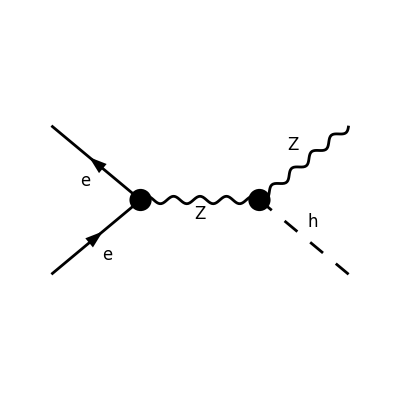

```mathematica
Paint[diagLO,ColumnsXRows->{2,1},Numbering->None];
```

```mathematica
FCClearScalarProducts[];
```

```mathematica
(*set the kinematics*)
```

```mathematica
SetMandelstam[s,t,u,p1,p2,-k1,-k2,0,0,MZ,mh];
```

```mathematica
(*define the matrix element*)
```

```mathematica
ampLO[0]=FCFAConvert[CreateFeynAmp[diagLO,PreFactor->1],IncomingMomenta->{p1,p2},OutgoingMomenta->{k1,k2},TransversePolarizationVectors->{k1},ChangeDimension->D,Contract->True,UndoChiralSplittings->True,List->False,DropSumOver->False,LorentzIndexNames->{µ,ν},FinalSubstitutions->{gc44->(FCGV["EL"]^2*v)/(2*FCGV["CW"]^2*FCGV["SW"]^2)}]/.FCGV[x_String]:>ToExpression[x]//FCGVToSymbol//DiracSimplify[#,DiracSubstitute67->False]&;
```

```mathematica
(*matrix element squared*)
```

```mathematica
ampLOSquared[0]=ampLO[0]( ComplexConjugate[ampLO[0]])//FeynAmpDenominatorExplicit//FermionSpinSum[#,ExtraFactor->1/2^2]&//DiracSimplify//DoPolarizationSums[#,k1]&//FCReplaceD[#,D->4]&//TrickMandelstam[#,{s,t,u,MZ^2+mh^2}]& //DiracSimplify;
```

```mathematica
(*This is just to check Eq.(3.7)*)
```

```mathematica
ampLO[0]( ComplexConjugate[ampLO[0]])/.ME->0//FeynAmpDenominatorExplicit//FermionSpinSum[#,ExtraFactor->1/2^2]&//DiracSimplify//DoPolarizationSums[#,k1]&//FCReplaceD[#,D->4]&//DiracSimplify//FullSimplify//TraditionalForm
```

(EL^4 v^2 (gc54L^2+gc54R^2) (MZ^4+MZ^2 (s-t-u)+t u))/(16 CW^4 SW^4 (MZ^3-MZ s)^2)

```mathematica
(*This allows us to simplify expressions in terms of the least number of Mandelstam variables:*)
```

```mathematica
TrickMandelstam[-MZ^2(t+u)+MZ^4,{s,t,u,MZ^2+mh^2}]
```

-MZ^2 (mh^2-s)

```mathematica
(*Check finished*)
```

```mathematica
(*Continuation*)
```

```mathematica
M2[t_,u_,ME_]:=Evaluate[ampLOSquared[0]]
```

```mathematica
(*dσLO/dt=(1/(16 Pi s^2))|M|^2 where M is the matrix element. We integrate over t  and replace u from s+t+u=ME^2+ME^2+MZ^2+mh^2 and take ME=0*)
```

```mathematica
σIntegrated=1/(16 Pi s^2)*Integrate[M2[t,MZ^2+mh^2-s-t,0],t];
```

```mathematica
(*Källén function*)
λ[x_,y_,z_]:=x^2+y^2+z^2-2x y-2x z-2y z;
(*Kinematic limits for the integration in terms of κ=√λ, see definition of the Mandelstam variable t and take cosθ=±1*)
tUpper=1/2 (MZ^2+mh^2-s+κ);
tLower=1/2 (MZ^2+mh^2-s-κ);
```

```mathematica
(*LO cross section*)
σLOIntegrated=(σIntegrated/.t->tUpper)- (σIntegrated/.t->tLower);
```

```mathematica
(*Final expression in terms of same gv and ga couplings in the paper *)
```

```mathematica
σLO=(Numerator[σLOIntegrated]/.gc54L->(2 √2 ga)/.gc54R->(2 √2 gv))/Denominator[σLOIntegrated]//FullSimplify
```

(EL^4 (ga^2+gv^2) v^2 κ (3 (mh^4+MZ^4+6 MZ^2 s+s^2-2 mh^2 (MZ^2+s))-κ^2))/(384 CW^4 MZ^2 π (MZ^2-s)^2 s^2 SW^4)

```mathematica
%/.mh^4+MZ^4+6 MZ^2 s+s^2-2 mh^2 (MZ^2+s)->(κ^2+8s MZ^2)//Simplify
```

(EL^4 (ga^2+gv^2) v^2 κ (12 MZ^2 s+κ^2))/(192 CW^4 MZ^2 π (MZ^2-s)^2 s^2 SW^4)

```mathematica
(*The above substitution  /.mh^4+MZ^4+6 MZ^2 s+s^2-2 mh^2 (MZ^2+s)->(κ^2+8s MZ^2)can be checked by replacing the values in the Källén function, I did it by hand just because I wanted to explicitly see the same expression as in Michael's paper Eq.(3.2):*)
```

#### NLO

```mathematica
LoopTopo=CreateTopologies[1,2->2,ExcludeTopologies->{WFCorrections,AllBoxes,SelfEnergies}];
```

```mathematica
LoopDiag=InsertFields[LoopTopo,{-F[2,{1}],F[2,{1}]}->{V[2],S[1]},Model->{"tripletSM"},GenericModel->{"tripletSM"},InsertionLevel->{Particles},ExcludeParticles->{S[1],S[2],V[3|4],U[1|2|3|4|11|12|31|32],F[_,{_}]}];
```

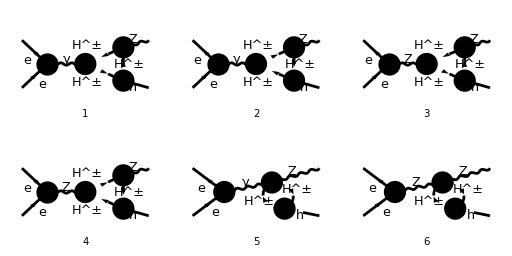

```mathematica
Paint[LoopDiag,ColumnsXRows->{3,2},Numbering->Simple,ImageSize->{512,256}];
```

```mathematica
ampsNLO[0]=FCFAConvert[CreateFeynAmp[LoopDiag,PreFactor->-I/(2Pi)^D],IncomingMomenta->{p1,p2},OutgoingMomenta->{k1,k2},LoopMomenta->{q},TransversePolarizationVectors->{k1},ChangeDimension->D,UndoChiralSplittings->True,List->True,DropSumOver->False,LorentzIndexNames->{µ,ν,µ1,ν1,µ2,ν2}]/.lam3->Subscript[λ, 3]/.gc54L->(2Sqrt[2]ga)/.gc54R->(2Sqrt[2]gv)/.gc11->Sqrt[2]*FCGV["EL"]/.gc38->(-2*FCGV["CW"]*FCGV["EL"])/FCGV["SW"]/.gc47->-FCGV["EL"]/.FCGV[x_String]:>ToExpression[x]//DiracSimplify[#,DiracSubstitute67->False]&//FCGVToSymbol;
```

```mathematica
(*Splitting the amplitudes into ZZ and γZ terms to simplify the analysis*)
```

```mathematica
ampsγZNLO[1]={ ampsNLO[0][[1]],ampsNLO[0][[2]],ampsNLO[0][[5]]};
```

```mathematica
ampsZZNLO[1]={ ampsNLO[0][[3]],ampsNLO[0][[4]],ampsNLO[0][[6]]};
```

```mathematica
(*Total of each contribution*)
```

```mathematica
ampsγZNLO[2] =Total[ampsγZNLO[1]];
```

```mathematica
ampsZZNLO[2] =Total[ampsZZNLO[1]];
```

```mathematica
(*Looking at equation 3.8 the PaVe functions factorize so we do not have to look at all diagrams to reproduce the calculation:*)
```

```mathematica
AmpNLOtest=TID[ampsZZNLO[2],q,UsePaVeBasis->True,ToPaVe->True]//DiracSimplify;
```

```mathematica
(*The LO amplitude has an "I" prefactor:*)
```

```mathematica
AmpLOtest=ComplexConjugate[I ampLO[0]]//DiracSimplify;
```

```mathematica
(*The following command allow us to use the Breitenlohner-Maison-’t Hooft-Veltman scheme when dealing with matrices in D dimensions, in particular to handle gamma5*)
```

```mathematica
FCSetDiracGammaScheme["BMHV"];
```

```mathematica
(*Product aiming to get Eq. 3.8*)
```

```mathematica
ampsquaredtest=AmpNLOtest AmpLOtest/.gc54L->(2Sqrt[2]ga)/.gc54R->(2Sqrt[2]gv)/.lam3->Subscript[λ, 3]/.MH0->Subscript[M, H]/.MHch->Subscript[M, Hp]/.gc44->(FCGV["EL"]^2*v)/(2*FCGV["CW"]^2*FCGV["SW"]^2)//FCGVToSymbol/.ME->0//FeynAmpDenominatorExplicit//FermionSpinSum[#,ExtraFactor->1/2^2]& //DoPolarizationSums[#,k1]&//FCReplaceD[#,D->4-2Epsilon]&//Series[#,{Epsilon,0,0}]&//Normal//ChangeDimension[#,4]&//DiracSimplify;
```

```mathematica
(*The following Eps[Momentum[k1],Momentum[k2],Momentum[p1],Momentum[p2]]->0 gets rid of the imaginary part of the product*)
```

```mathematica
Reampsquaredtest=ampsquaredtest/.Eps[Momentum[k1],Momentum[k2],Momentum[p1],Momentum[p2]]->0/.ME^2->0//TrickMandelstam[#,{s,t,u,MZ^2+mh^2}]&;
```

```mathematica
(*The resultant expression is given in terms of tensor PaVe functions and looks simple enough... I will try(cry) to get numerical results from here while you check that the algebra matches*)
```

```mathematica
Reampsquaredtest//FullSimplify//TraditionalForm
```

1/(8 π^2 MZ^2 SW^4 (MZ^2-s)^2)EL^4 λ_3 v^2 (ga^2+gv^2) ((mh^2 MZ^2+2 MZ^4-2 MZ^2 (t+u)+t u) B_0(mh^2,M_Hp^2,M_Hp^2)-8 (2 (mh^2 MZ^2+2 MZ^4-2 MZ^2 (t+u)+t u) C_00(mh^2,MZ^2,s,M_Hp^2,M_Hp^2,M_Hp^2)+(2 MZ^2-t-u) (mh^2 MZ^2-t u) C_1(mh^2,s,MZ^2,M_Hp^2,M_Hp^2,M_Hp^2)+(2 MZ^2-t-u) (mh^2 MZ^2-t u) (C_11(mh^2,s,MZ^2,M_Hp^2,M_Hp^2,M_Hp^2)+C_12(mh^2,s,MZ^2,M_Hp^2,M_Hp^2,M_Hp^2))))

#### Simplified expressions

```mathematica
(*We can look at the PaVe part alone*)
```

```mathematica
Pavepart=(1/(8 MZ^2  π^2 SW^4(MZ^2-s)^2) EL^4 Subscript[λ, 3] v^2(ga^2+gv^2)   )^-1 Reampsquaredtest;
```

```mathematica
(*Writing down the Pavepart in terms of scalars PaVe functions A0,B0,C0 with the //PaVeReduce command:*)
```

```mathematica
Pavepart=Pavepart/.u->MZ^2+mh^2-s-t//PaVeReduce//FCReplaceD[#,D->4]&;
```

```mathematica
Pavepart//FullSimplify//TraditionalForm
```

1/((mh^4-2 (MZ^2+s) mh^2+(MZ^2-s)^2)^2)(-8 s ((2 t-3 MZ^2) mh^6+(MZ^4+(5 s+4 t) MZ^2-2 t (3 s+t)) mh^4+(MZ^6-2 t MZ^4-(s^2+4 t s+2 t^2) MZ^2+2 s t (3 s+2 t)) mh^2+(MZ^2-s) (MZ^6-2 (s+2 t) MZ^4+(s^2+2 t s+4 t^2) MZ^2+2 s t (s+t))) B_0(MZ^2,M_Hp^2,M_Hp^2) MZ^2+8 s ((2 MZ^2+s-2 t) mh^6+(-4 MZ^4+(s+2 t) MZ^2-3 s^2+2 t^2) mh^4+(2 MZ^6+(s+2 t) MZ^4-2 (3 s^2+4 t s+2 t^2) MZ^2+s (3 s^2+6 t s+2 t^2)) mh^2+(MZ^2-s) ((s-2 t) MZ^4-2 (s^2+t s-t^2) MZ^2+s (s+2 t)^2)) B_0(s,M_Hp^2,M_Hp^2) MZ^2-8 s C_0(mh^2,MZ^2,s,M_Hp^2,M_Hp^2,M_Hp^2) ((MZ^2-t) mh^8+(-MZ^4+s MZ^2+t (2 s+t)) mh^6-(MZ^6-2 (s+t) MZ^4+(s+t) (5 s+t) MZ^2+s t^2) mh^4+(MZ^8+s MZ^6-(s+t) (5 s+t) MZ^4+s (3 s^2+8 t s+6 t^2) MZ^2-s^2 t (2 s+t)) mh^2+2 ((mh-MZ)^2-s) ((mh+MZ)^2-s) (mh^4-2 (s+t) mh^2+MZ^4+s^2+2 t^2+2 s t-2 MZ^2 (s+t)) M_Hp^2-(MZ^2-s)^2 (MZ^2+s) (MZ^2-s-t) t) MZ^2+(3 (MZ^2-t) mh^10+3 (-4 MZ^4+3 (t-2 s) MZ^2+t (5 s+t)) mh^8+2 (9 MZ^6-(2 s+3 t) MZ^4+(17 s^2+10 t s-6 t^2) MZ^2-3 s t (5 s+2 t)) mh^6-2 (6 MZ^8+(3 t-8 s) MZ^6-(10 s^2+5 t s+9 t^2) MZ^4+s (12 s^2+33 t s+10 t^2) MZ^2-3 s^2 t (5 s+3 t)) mh^4+((3 MZ^2+s) (MZ^2+3 s) (MZ^3-MZ s)^2-4 (MZ^2-3 s) (3 MZ^2-s) (MZ^2+s) t^2+(MZ^2-s) (9 MZ^6-35 s MZ^4-21 s^2 MZ^2+15 s^3) t) mh^2+(MZ^2-s)^2 (2 s (MZ^3-MZ s)^2+(3 MZ^2+s) (MZ^2+3 s) t^2-(MZ^2-s) (3 MZ^2+s) (MZ^2+3 s) t)) B_0(mh^2,M_Hp^2,M_Hp^2))

```mathematica
(*The expression is quite complicated to compare but has the shape, let's see term by term, starting with B0(s)*)
```

```mathematica
(*Factor of two from 2 times real part*)
```

```mathematica
B0sterm=2Coefficient[Pavepart, PaVe[0,{s},{Subscript[M, Hp]^2,Subscript[M, Hp]^2}]]//TrickMandelstam[#,{s,t,u,MZ^2+mh^2}]&//Expand//Simplify
```

-(16 MZ^2 s (2 mh^4 MZ^2 (4 MZ^2-t-u)-mh^2 (t^3+8 MZ^2 t u-3 t^2 u-3 t u^2+u^3+2 MZ^4 (t+u))+(t+u) ((t-u)^2 (t+u)-MZ^2 (t^2-4 t u+u^2))))/((-2 mh MZ+t+u)^2 (2 mh MZ+t+u)^2)

```mathematica
(*These are the B_0 factors from Eq.3.8, -8 from 4*2 in numerator of 3.8 *)
```

```mathematica
B0stermMichael=-8((t u +2s MZ^2 -mh^2MZ^2)(mh^4+(MZ^2-s)^2-2 mh^2 (MZ^2+s))^-1(s*(-Mh^2-MZ^2+s)-(M1^2-M2^2)*(Mh^2-MZ^2+s))+

(s+MZ^2-mh^2)(mh^2MZ^2-t u)(mh^4+(MZ^2-s)^2-2 mh^2 (MZ^2+s))^-2(((Mh^2-3*MZ^2)*(Mh^2-MZ^2)^2-(3*Mh^4+MZ^4)*s+(3*Mh^2+5*MZ^2)*s^2-s^3+(1/s)*(M1^2-M2^2)*((Mh^2-MZ^2)^3-5*(Mh^4-MZ^4)*s+(7*Mh^2-MZ^2)*s^2-3*s^3))-

(Mh^6-(MZ^2-s)^2*(3*MZ^2+2*s)-Mh^4*(5*MZ^2+4*s)+Mh^2*(7*MZ^4-4*MZ^2*s+5*s^2)+(M1^2-M2^2)*((Mh^2-MZ^2)^2+2*(-3*Mh^4+Mh^2*MZ^2+2*MZ^4)*s+(3*Mh^2-5*MZ^2)*s^2+2*s^3)))/.Mh->mh/.M1->Subscript[M, Hp]/.M2->Subscript[M, Hp])//TrickMandelstam[#,{s,t,u,MZ^2+mh^2}]&//Expand//Simplify
```

-(16 MZ^2 s (2 mh^4 MZ^2 (4 MZ^2-t-u)-mh^2 (t^3+8 MZ^2 t u-3 t^2 u-3 t u^2+u^3+2 MZ^4 (t+u))+(t+u) ((t-u)^2 (t+u)-MZ^2 (t^2-4 t u+u^2))))/((-2 mh MZ+t+u)^2 (2 mh MZ+t+u)^2)

```mathematica
(*Check if they match*)
```

```mathematica
B0stermMichael== B0sterm//TrickMandelstam[#,{s,t,u,MZ^2+mh^2}]&//Expand//Simplify
```

True

```mathematica
(*They do match!!!*)
```

### Work in progress

```mathematica
(*DO NOT TRUST MY MICHAEL EXPRESSIONS BELOW, THEY ARE INCOMPLETE*)
```

```mathematica
(*Now let's see B0(k1)=B0(MZ^2)*)
```

```mathematica
B0k1term=2Coefficient[Pavepart,PaVe[0,{MZ^2},{Subscript[M, Hp]^2,Subscript[M, Hp]^2}]]//TrickMandelstam[#,{s,t,u,MZ^2+mh^2}]&//Expand//Simplify
```

-(8 MZ^2 s (4 mh^4 MZ^4+(t+u) (2 t u (t+u)+MZ^2 (t^2-4 t u+u^2))+2 mh^2 (MZ^4 (t+u)-2 MZ^2 (t^2+t u+u^2))))/((-2 mh MZ+t+u)^2 (2 mh MZ+t+u)^2)

```mathematica
B0k1termMichael=-4((t u +2s MZ^2 -mh^2MZ^2)(mh^4+(MZ^2-s)^2-2 mh^2 (MZ^2+s))^-1(-(MZ^2 (Mh^2-MZ^2+s)+(M1^2-M2^2) (Mh^2+MZ^2-s)))+

(s+MZ^2-mh^2)(mh^2MZ^2-t u)(mh^4+(MZ^2-s)^2-2 mh^2 (MZ^2+s))^-2((-6 MZ^2 (MZ^2 (Mh^2-MZ^2+s)+(M1^2-MZ^2) (Mh^2+MZ^2-s)))-

((MZ^2 (-Mh^4+5 (MZ^2-s)^2-4 Mh^2 (MZ^2+s))-(M1^2-M2^2) (Mh^4+(MZ^2-s)^2+2 Mh^2 (5 MZ^2-s)))))/.Mh->mh/.M1->Subscript[M, Hp]/.M2->Subscript[M, Hp])//TrickMandelstam[#,{s,t,u,MZ^2+mh^2}]&//Expand//Simplify
```

-1/((-2 mh MZ+t+u)^2 (2 mh MZ+t+u)^2)8 MZ^2 (4 mh^6 MZ^4+2 mh^4 MZ^2 (2 MZ^4-MZ^2 (t+u)-2 (t^2+t u+u^2))-(t+u) (2 t u (t+u)^2-MZ^4 (t^2-10 t u+u^2)+MZ^2 (t^3-8 t^2 u-8 t u^2+u^3))+mh^2 (8 MZ^6 (t+u)+2 t u (t+u)^2-MZ^4 (9 t^2+14 t u+9 u^2)+5 MZ^2 (t^3+t^2 u+t u^2+u^3))-3 (2 MZ^2-t-u) (t+u) (mh^2 MZ^2-t u) M_Hp^2)

```mathematica
(*Now let's see C0*)
```

```mathematica
C0termMichael=-8((*(t u +2s MZ^2 -mh^2MZ^2)2(mh^4+(MZ^2-s)^2-2 mh^2 (MZ^2+s))^-1(1/4)2(Mh^2*MZ^2*s+(M1^4+M2^4)*Mh^2+M1^2*Mh^2*(Mh^2-MZ^2-s)+M2^2*((MZ^2-s)^2-Mh^2*(MZ^2+s))-2*M1^2*M2^2*Mh^2)+*)

(s+MZ^2-mh^2)(mh^2MZ^2-t u)(1/2)(mh^4+(MZ^2-s)^2-2 mh^2 (MZ^2+s))^-2(2*(MZ^4*(Mh^4-2*Mh^2*(MZ^2-2*s)+(MZ^2-s))+(M1^4+M2^4)*(Mh^4+2*Mh^2*(2*MZ^2-s)+(MZ^2-s)^2)-2*MZ^2*(Mh^4*(-2*M1^2+M2^2)+(MZ^2-s)^2*(M1^2-2*M2^2)+Mh^2*(MZ^2+s)*(M1^2+M2^2))-2*M1^2*M2^2*(Mh^4+2*Mh^2*(2*MZ^2-s)+(MZ^2-s)^2))-

2*(MZ^2*((MZ^2-s)^3+Mh^4*(MZ^2+2*s)-Mh^2*(2*MZ^4-3*MZ^2*s+2*s^2)))+3*((M1^4+M2^4)*Mh^2*(Mh^2+MZ^2-s)+M1^2*(Mh^2-MZ^2+s)*(Mh^4+2*Mh^2*(2*MZ^2-s)+(MZ^2-s)^2))+
2*M2^2*((MZ^2-s)^3-Mh^4*(2*MZ^2+s)+Mh^2*(MZ^4-3*MZ^2*s+2*s^2))-6*M1^2*M2^2*Mh^2*(Mh^2+MZ^2-s)/.Mh->mh/.M1->Subscript[M, Hp]/.M2->Subscript[M, Hp]))//TrickMandelstam[#,{s,t,u,MZ^2+mh^2}]&//FullSimplify//TraditionalForm
```

-1/(((t+u)^2-4 mh^2 MZ^2)^2)4 (2 MZ^2-t-u) (mh^2 MZ^2-t u) (M_Hp^2 (3 mh^6+mh^4 (9 MZ^2-5 s)+mh^2 (-15 MZ^4-2 MZ^2 s+s^2)+(MZ^2-s)^2 (3 MZ^2+s))+2 MZ^2 (MZ^2 s (mh^2-3 s-1)+s (-2 mh^4+2 mh^2 s+s^2)-MZ^6+MZ^4 (3 s+1)))

```mathematica
C0term=2Coefficient[Pavepart,PaVe[0,{mh^2,MZ^2,s},{Subscript[M, Hp]^2,Subscript[M, Hp]^2,Subscript[M, Hp]^2}]]//TrickMandelstam[#,{s,t,u,MZ^2+mh^2}]&//FullSimplify//TraditionalForm
```

1/(((t+u)^2-4 mh^2 MZ^2)^2)8 MZ^2 s (-2 M_Hp^2 (2 mh MZ-t-u) (2 mh MZ+t+u) (2 mh^2 MZ^2-t^2-u^2)+4 mh^6 MZ^4+4 mh^4 MZ^2 (MZ^4-t^2-t u-u^2)+mh^2 (-4 MZ^4 (t^2+t u+u^2)+MZ^2 (t+u) (3 t^2-2 t u+3 u^2)+2 t u (t+u)^2)-t u (t+u)^2 (-2 MZ^2+t+u))

#### couplings mapping

```mathematica
(*comparison of couplings from the .mod file and the ones in Michael's paper after Eq.3.1*)
```

```mathematica
(*/.gc51L->-1/2*(FCGV["EL"]*(FCGV["CW"]^2-FCGV["SW"]^2))/(FCGV["CW"]*FCGV["SW"])/.gc51R->(FCGV["EL"]*FCGV["SW"])/FCGV["CW"]//FCGVToSymbol*)
```

```mathematica
(*/.gL->-1/2*EL((FCGV["CW"]^2-FCGV["SW"]^2))/(FCGV["CW"]*FCGV["SW"])/.gR->EL(FCGV["SW"])/FCGV["CW"]//FCGVToSymbol*)
```

```mathematica
gv=(-1/2+2Sin[x]^2)/(2);ga=(-1/(4));
```

```mathematica
gL=(-1/2)((Cos[x]^2-Sin[x]^2));gR=Sin[x]^2;
```

```mathematica
gv^2+ga^2//FullSimplify
```

1/8 (2-2 Cos[2 x]+Cos[4 x])

```mathematica
(gL^2+gR^2)//FullSimplify
```

1/4 (2-2 Cos[2 x]+Cos[4 x])

```mathematica
Clear[gv,ga,gL,gR]
```

```mathematica
(*ampsquaredtest=ampsquaredtest/. DiracTrace->(DiracTrace[#,DiracTraceEvaluate->True]&)/.Eps[Momentum[k1],Momentum[k2],Momentum[p1],Momentum[p2]]->0;*)
```

```mathematica
(*s->MZ^2+mh^2-t-u*)
```

```mathematica
(*/.-MZ^2(t+u)+MZ^4->-MZ^2 (mh^2-s)*)
```

```mathematica
(*//TrickMandelstam[#,{s,t,u,MZ^2+mh^2}]&*)
```